Number of points = 6

Initial divided differences table:

(5 | -8/3 | 7/12 | -181/3900 | 563/327600 | -0.000566147
-3 | 2 | -1/50 | -161/15600 | -0.0104536 | 0
7 | 9/5 | -107/520 | -0.203712 | 0 | 0
16 | -7/8 | -2.95588 | 0 | 0 | 0
9 | -26. | 0 | 0 | 0 | 0
-4 | 0 | 0 | 0 | 0 | 0)

Final divided differences table:

(5 | -8/3 | 7/12 | -181/3900 | 563/327600 | -0.000566147
-3 | 2 | -1/50 | -161/15600 | -0.0104536 | 0
7 | 9/5 | -107/520 | -0.203712 | 0 | 0
16 | -7/8 | -2.95588 | 0 | 0 | 0
9 | -26. | 0 | 0 | 0 | 0
-4 | 0 | 0 | 0 | 0 | 0)

Interpolating polynomial:

5-(8 (1+x))/3+7/12 (-2+x) (1+x)-(181 (-7+x) (-2+x) (1+x))/3900+(563 (-12+x) (-7+x) (-2+x) (1+x))/327600-0.000566147 (-20+x) (-12+x) (-7+x) (-2+x) (1+x)

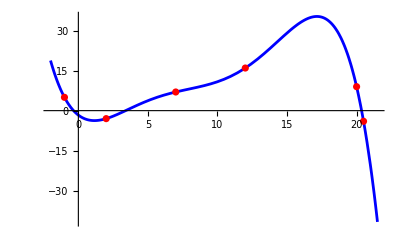

```mathematica
DivDifInterpolation[xvalues_List,yvalues_List]:=Module[{n,DivDif,poly,term,q,f,p},n=Length[xvalues];
DivDif=Table[0,{n},{n}];
Do[DivDif[[i,1]]=yvalues[[i]],{i,1,n}];
Quiet[Do[Do[DivDif[[i,j]]=(DivDif[[i+1,j-1]]-DivDif[[i,j-1]])/(xvalues[[i+j-1]]-xvalues[[i]]),{i,1,n-j+1}],{j,2,n}];];
term=1;
poly=DivDif[[1,1]];
Do[term*=(x-xvalues[[i]]);
poly+=DivDif[[1,i+1]]*term,{i,1,n-1}];
q=ListPlot[Transpose[{xvalues,yvalues}],PlotStyle->Red];
f[x_]:=poly;
p=Plot[f[x],{x,Min[xvalues]-1,Max[xvalues]+1},PlotStyle->Blue];
Print["Number of points = ",n];
Print["Initial divided differences table:"];
Print[MatrixForm[DivDif]];
Print["Final divided differences table:"];
Print[MatrixForm[DivDif]];
Print["Interpolating polynomial:"];
Print[poly];
{poly,Show[p,q]}];

(*Example usage*)
{interpollation,plt}=DivDifInterpolation[{-1,2,7,12,20,20.5},{5,-3,7,16,9,-4}];

Print[plt]
```

Number of points = 9

Initial divided differences table:

(1 | -4/π | 0 | 64/(3 π^3) | -128/(3 π^4) | 512/(15 π^5) | 0 | -8192/(315 π^7) | 8192/(315 π^8)
0 | -4/π | 16/π^2 | -64/(3 π^3) | 0 | 512/(15 π^5) | -2048/(45 π^6) | 8192/(315 π^7) | 0
-1 | 4/π | 0 | -64/(3 π^3) | 128/(3 π^4) | -512/(15 π^5) | 0 | 0 | 0
0 | 4/π | -16/π^2 | 64/(3 π^3) | 0 | -512/(15 π^5) | 0 | 0 | 0
1 | -4/π | 0 | 64/(3 π^3) | -128/(3 π^4) | 0 | 0 | 0 | 0
0 | -4/π | 16/π^2 | -64/(3 π^3) | 0 | 0 | 0 | 0 | 0
-1 | 4/π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/π | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Final divided differences table:

(1 | -4/π | 0 | 64/(3 π^3) | -128/(3 π^4) | 512/(15 π^5) | 0 | -8192/(315 π^7) | 8192/(315 π^8)
0 | -4/π | 16/π^2 | -64/(3 π^3) | 0 | 512/(15 π^5) | -2048/(45 π^6) | 8192/(315 π^7) | 0
-1 | 4/π | 0 | -64/(3 π^3) | 128/(3 π^4) | -512/(15 π^5) | 0 | 0 | 0
0 | 4/π | -16/π^2 | 64/(3 π^3) | 0 | -512/(15 π^5) | 0 | 0 | 0
1 | -4/π | 0 | 64/(3 π^3) | -128/(3 π^4) | 0 | 0 | 0 | 0
0 | -4/π | 16/π^2 | -64/(3 π^3) | 0 | 0 | 0 | 0 | 0
-1 | 4/π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/π | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Interpolating polynomial:

1-(4 (π+x))/π+(64 (π/2+x) ((3 π)/4+x) (π+x))/(3 π^3)-(128 (π/4+x) (π/2+x) ((3 π)/4+x) (π+x))/(3 π^4)+(512 x (π/4+x) (π/2+x) ((3 π)/4+x) (π+x))/(15 π^5)-(8192 x (-π/2+x) (-π/4+x) (π/4+x) (π/2+x) ((3 π)/4+x) (π+x))/(315 π^7)+(8192 x (-(3 π)/4+x) (-π/2+x) (-π/4+x) (π/4+x) (π/2+x) ((3 π)/4+x) (π+x))/(315 π^8)

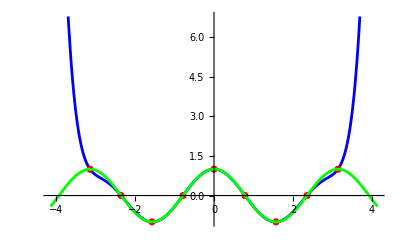

```mathematica
(*Sampling and visualizing for Cos[2x]*)

xvalues=Table[x,{x,-Pi,Pi,Pi/4}];
yvalues=Table[Cos[2*x],{x,-Pi,Pi,Pi/4}];
{interpollationCos2x,pltcos2x}=DivDifInterpolation[xvalues,yvalues];
g[x_]=Cos[2 x];
r=Plot[g[x],{x,Min[xvalues]-1,Max[xvalues]+1},PlotStyle->Green];
Show[pltcos2x,r]
```